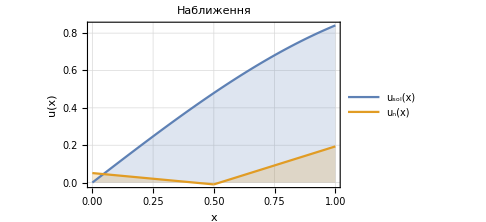

q={0.0509716,-0.00982268,0.193611}

F={0.0411489,0.23476,0.183789}

K=(1 | 1 | 0
1 | 1 | 1
0 | 1 | 1)

```mathematica
a=0;b=1;f[x_]:=Sin[x];
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
u0 = 0; u1 = Cos[1];
$MaxPiecewiseCases=700;
Subscript[u, sol]=NDSolveValue[{-(μ'[x]*u'[x]+μ[x] u''[x])+β[x] u'[x]+σ[x] u[x]==f[x],u[a]==u0,u'[b]==u1},u,{x,a,b}];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x],{x,a,b},FrameLabel->{"x ","u_sol(x) "},PlotLabel->Style[Framed["Наближення u_sol(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Subscript[u, sol]'[x],{x,a,b},FrameLabel->{"x ","u_sol'(x) "},PlotLabel->Style[Framed["Наближення u_sol'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=Sqrt[NIntegrate[Subscript[u, sol][x]^2,{x,a,b}]];
Subscript[norma2u, sol]=Sqrt[NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}]];
Print[Subscript[plot1u, sol],"  ",  Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
resfunc[x_] = Sin[x];
Print[Plot[y=resfunc[x] ,{x,a,b}, FrameLabel->{"x ","y "},PlotLabel->Style[Framed["Графік sin(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium], "   ", Plot[y=resfunc'[x],{x,a,b}, FrameLabel->{"x ","y "},PlotLabel->Style[Framed["Графік sin'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium]];
ϕ[x0_,i0_] :=
Module[{x=x0, i=i0, k, m},k=i+1; m=i-1;
Piecewise[{{
Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧}, {0,x<w⟦i⟧ || x>w⟦k⟧}}],
i≠ 1 && i≠n+1}, {Piecewise[{{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧},{0,x>w⟦k⟧}}], i==1},
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{0,x<w⟦i⟧}}], i==n+1}}]
];
n = 2;
h = (b-a)/n;
w = Table[a+i*h, {i,0,n}];

tabela = {{"1","2","3","4","5","6","7","8","9"}};
Print["##################################################################[----FEM n=",n," h=",h,"----]####################################################################"];
n1 = n+1;
matrixK = 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->1
(*NIntegrate[(μ[x]*ϕ'[x,i]*ϕ'[x,j]+β[x]*ϕ'[x,j]*ϕ[x,i]+σ[x]*ϕ[x,i]*ϕ[x,j]),
{x,a,b}, Method->"DoubleExponential"]*)}, {n1,n1},0];
Print["K=",MatrixForm[matrixK]];
F = Table[NIntegrate[f[x]*ϕ[x,i],{x,a,b}], {i,1,n1}];
Print["F=",F];
q = LinearSolve[matrixK,F];
Print["q=",q];
Subscript[u, n][x_]:=∑_(i=1)^(n+1) q[[i]]*ϕ[x,i];
difference = Plot[{Subscript[u, sol][x], Subscript[u, n][x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];

Print[difference];
```